En Mathematica podemos usar la función Plot3D para visualizar superficies en el espacio .

```mathematica
Plot3D[x^2+y^2,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

En Mathematica podemos usar la función Complex y Complex3D para visualizar funciones complejas en plano y en el espacio respectivamente.

```mathematica
ComplexPlot[Abs[z]^2,{z,-2-2 I,2+2 I}]
```

-Graphics-

```mathematica
ComplexPlot3D[Abs[z]^2,{z,-2-2 I,2+2 I}, ColorFunction->"CyclicLogAbs"]
```

-Graphics3D-

Para ver las curvas de nivel de las partes real e imaginaria de una usamos ComplexContourPlot

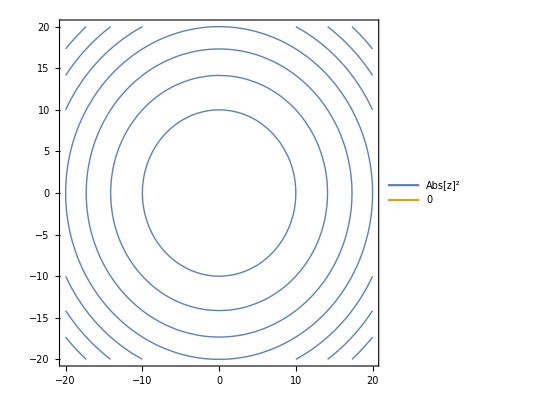

```mathematica
ComplexContourPlot[{Re[Abs[z]*Abs[z]],Im[Abs[z]*Abs[z]]},{z,20},PlotLegends->"Expressions"]
```

Ejemplo 2

-Graphics-

-Graphics3D-

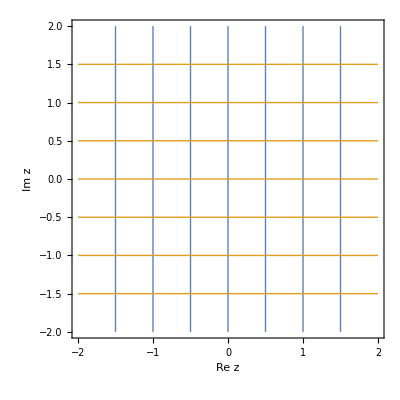

```mathematica
ComplexPlot[z,{z,-2-2 I,2+2 I}]
ComplexPlot3D[z,{z,-2-2 I,2+2 I}]
ComplexContourPlot[{Re[z],Im[z]},{z,2},FrameLabel->{Style["Re z",16],Style["Im z",16]}]
```

Ejemplo 3

```mathematica
ComplexPlot[Conjugate[z],{z,-2-2 I,2+2 I}]
ComplexPlot3D[Conjugate[z],{z,-2-2 I,2+2 I}]
ComplexContourPlot[{Re[Conjugate[z]],Im[Conjugate[z]]},{z,2},FrameLabel->{Style["Re z",16],Style["Im z",16]}]
```

-Graphics-

-Graphics3D-

-Graphics-

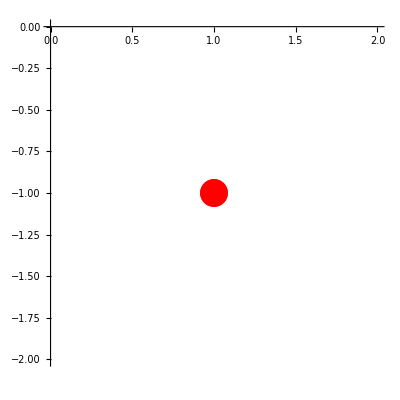

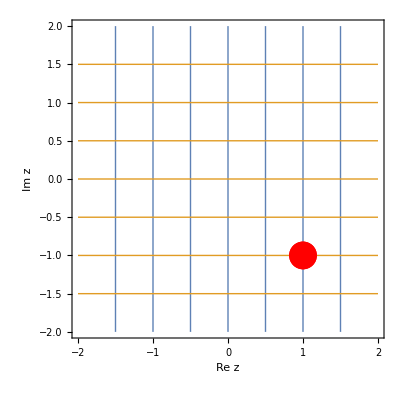

```mathematica
punto=ComplexListPlot[{Conjugate[1+1I]},PlotStyle->{Red,PointSize[0.05]} ]
Show[ComplexContourPlot[{Re[Conjugate[z]],Im[Conjugate[z]]},{z,2},FrameLabel->{Style["Re z",16],Style["Im z",16]}],punto]
```

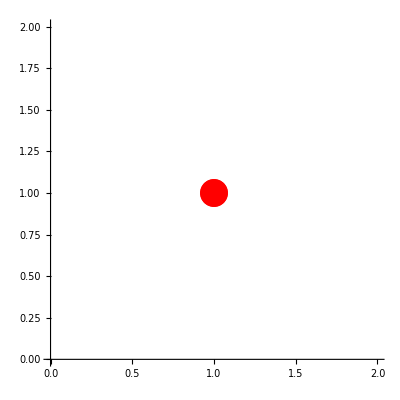

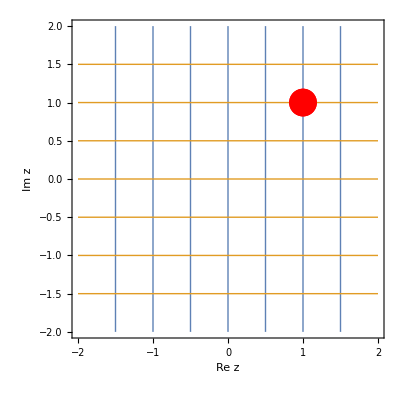

```mathematica
punto=ComplexListPlot[{1+1I},PlotStyle->{Red,PointSize[0.05]} ]
Show[ComplexContourPlot[{Re[z],Im[z]},{z,2},FrameLabel->{Style["Re z",16],Style["Im z",16]}],punto]
```

Ejemplo 4

Iy+x

-Graphics-

-Graphics3D-

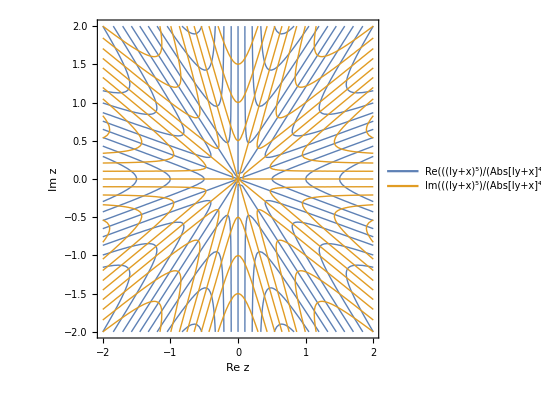

```mathematica
z=x+Iy
ComplexPlot[(z)^5/((Abs[z])^4),{z,-2-2 I,2+2 I}]
ComplexPlot3D[(z)^5/((Abs[z])^4),{z,-2-2 I,2+2 I}]
ComplexContourPlot[{Re[(z)^5/((Abs[z])^4)],Im[(z)^5/((Abs[z])^4)]},{z,2},FrameLabel->{Style["Re z",16],Style["Im z",16]},PlotLegends->"Expressions"]
```